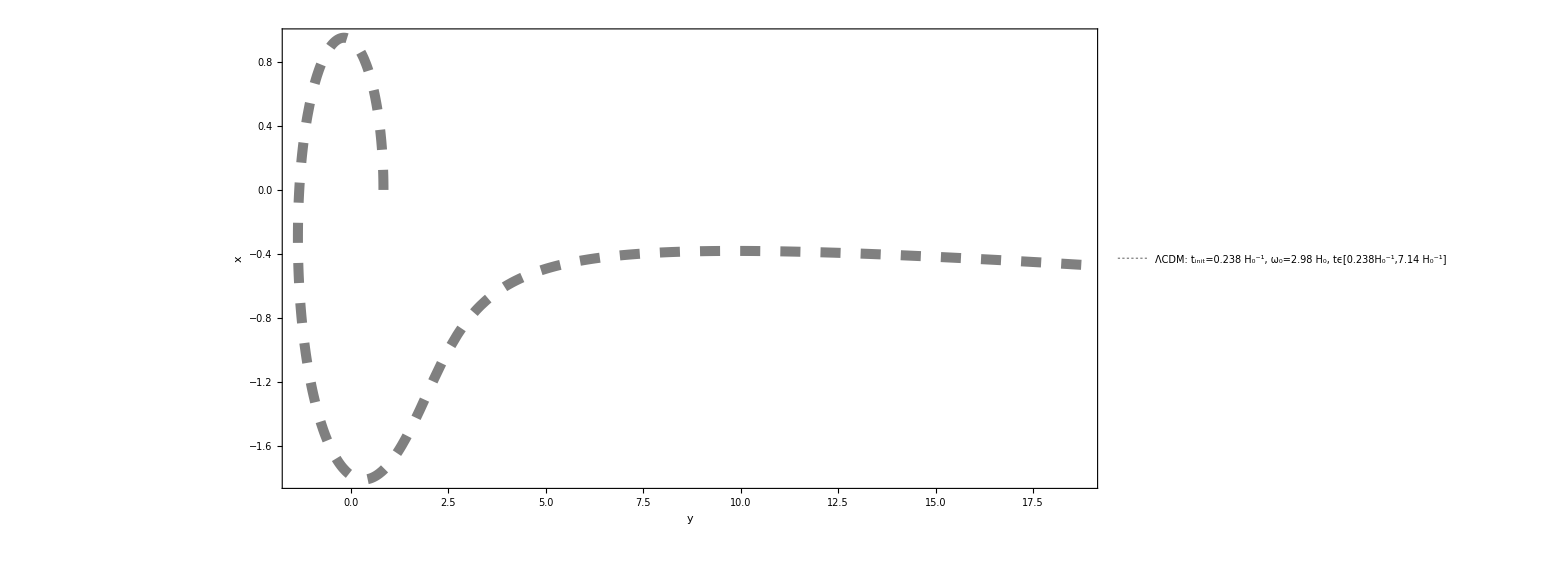

```mathematica
Off[NIntegrate::nlim,FunctionInterpolation::ncvb,NIntegrate::slwcon,NIntegrate::ncvb];
Clear[H0tinit,omegam,om];
H0tinit=0.238;  omegam=0.29;  om=0.71;


tend=30; ti=1;  (* time limits *)

a=(omegam/(1-omegam))^(1/3)Sinh[3/2 H0tinit √(1-omegam)t]^(2/3);  

ff=H0tinit^2(1+(-1-1/(2 a^3)) omegam);
par=om^2 rr - om^2 -ff  rr^4 /. t->ti; (* factor proportional to the effective force in the geodesic equation *)
ss=Part[Solve[par==0,rr] //N,4,1,2];  (* find initial equilibrium point to use in the initial conditions to avoid oscillations in the solution *)
solution1=NDSolve[{r''[t]+(om^2/r[t]^2)(1-1/r[t])-ff r[t]==0,r[ti]==ss,r'[ti]==0},r,{t,ti,tend},MaxSteps->300000]; (* find radial geodesic *)

solr1[t1_]:=Part[Evaluate[r[t]/.solution1] /. t->t1,1];
solth1[t1_]:=NIntegrate[om/solr1[t]^2,{t,ti,t1}];
solri1=FunctionInterpolation[solr1[t],{t,ti,tend}];
solthi1=FunctionInterpolation[solth1[tt],{tt,ti,tend}];

t1=1;t2=30;
plor1=ParametricPlot[{solri1[t] Cos[solthi1[t]],solri1[t] Sin[solthi1[t]]},{t,t1,t2},AspectRatio->Automatic,PlotRange->All,Frame->True,FrameLabel->{"x/r_0","y/r_0"},PlotStyle -> {Gray,Dashing[0.01],Thickness[0.005]},PlotLegends->Placed[LineLegend[{Style["ΛCDM: \!\(\*SubscriptBox[\(t\), \(init\)]\)=0.238 \!\(\*SuperscriptBox[SubscriptBox[\(H\), \(0\)],\(-1\)]\), \!\(\*SubscriptBox[\(ω\), \(0\)]\)=2.98 H_0, tϵ[0.238\!\(\*SuperscriptBox[SubscriptBox[\(H\), \(0\)], \(-1\)]\),7.14 \!\(\*SuperscriptBox[SubscriptBox[\(H\), \(0\)], \(-1\)]\)]",FontSize->25]},LabelStyle->{FontSize->25}],{Left,Top}]];


Plot1=Show[plor1,PlotRange->All,Frame->True,FrameLabel->{"y","x"},BaseStyle->{Large,FontFamily->"Times",Italic},LabelStyle->Directive[Black,Large]]
```

General::munfl: Exp[-60926.6] is too small to represent as a normalized machine number; precision may be lost.

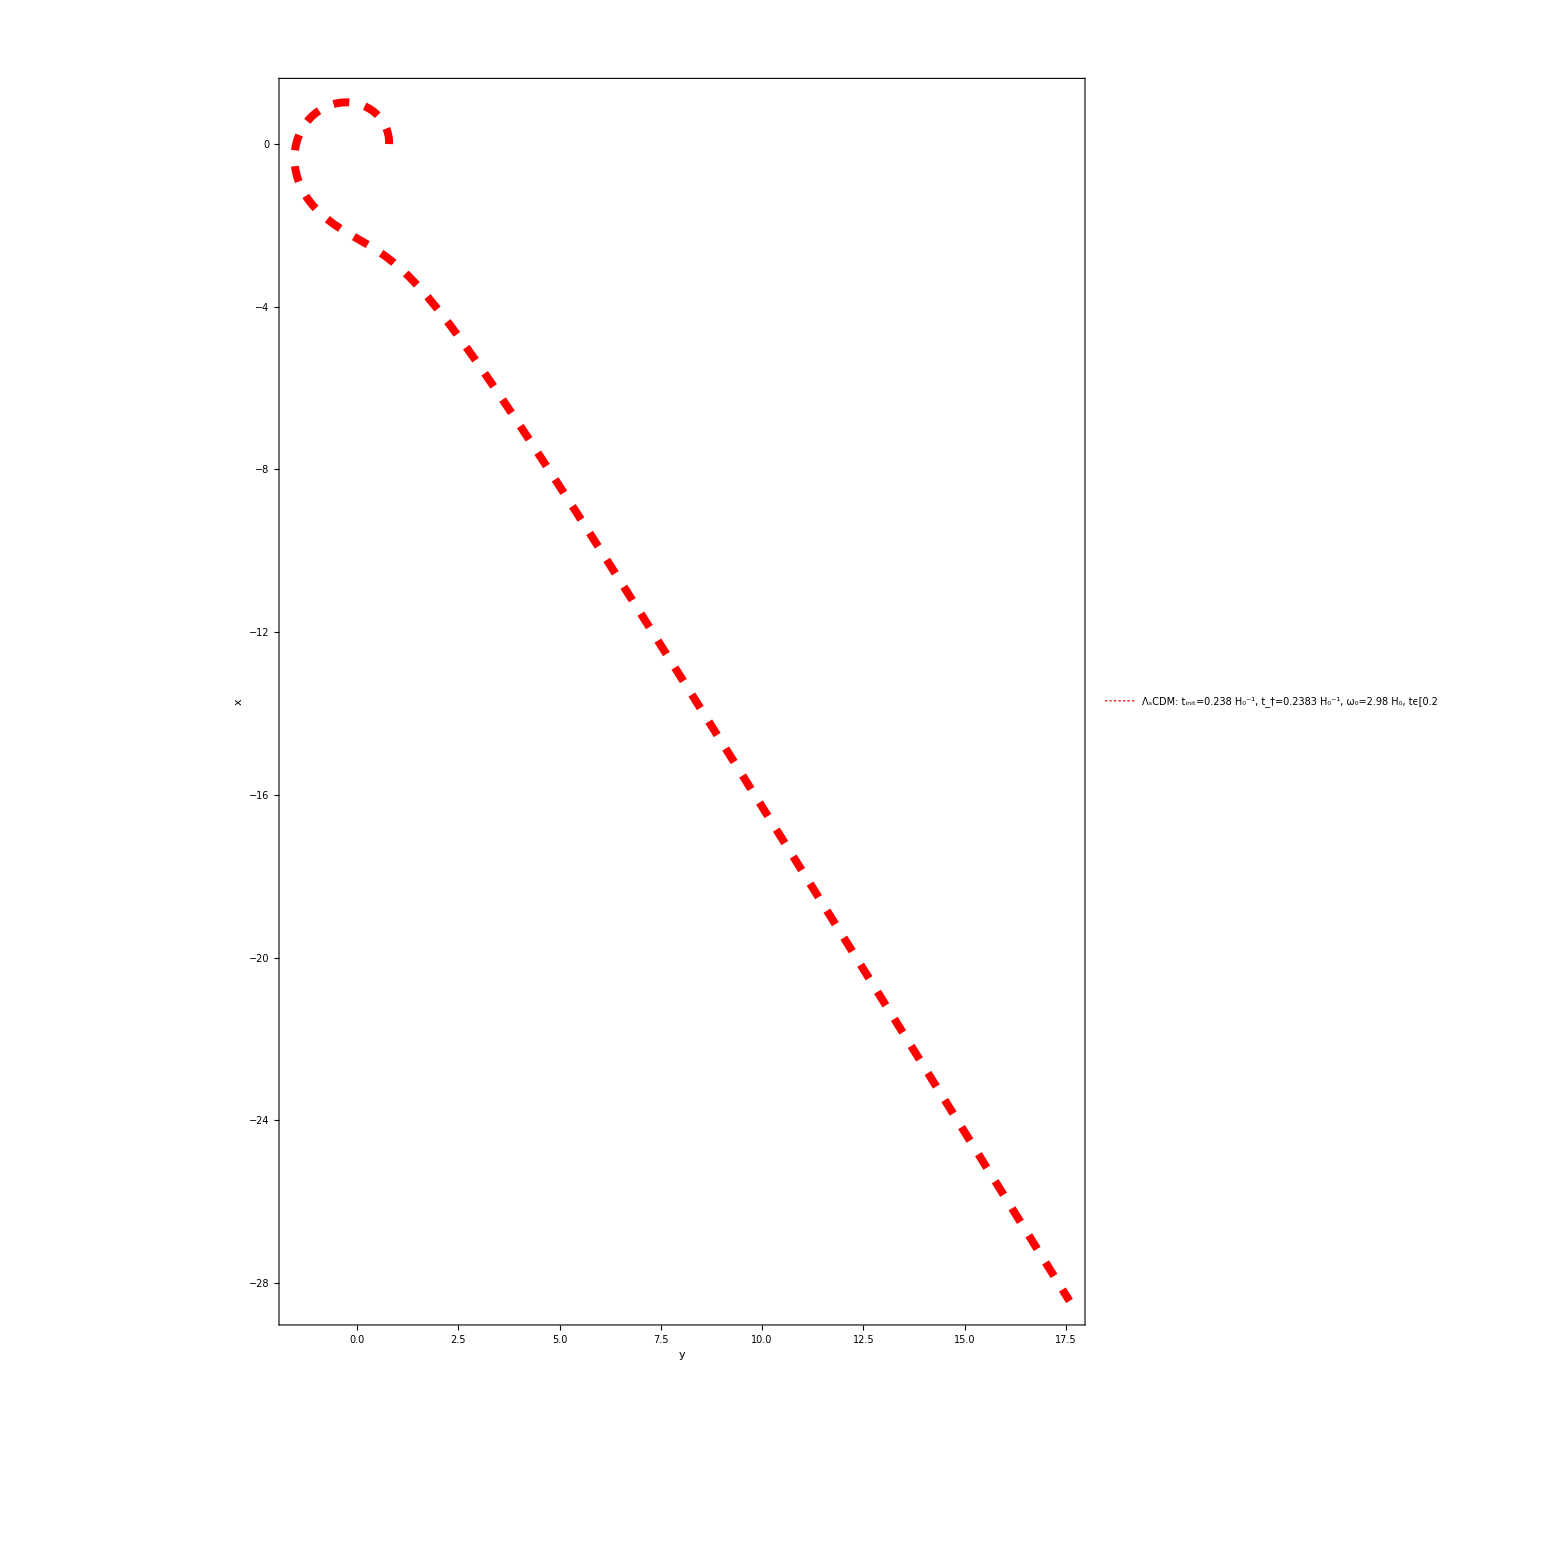

```mathematica
Off[NIntegrate::nlim,FunctionInterpolation::ncvb,NIntegrate::slwcon,NIntegrate::ncvb];
Clear[H0tinit,omegam,om];
H0tinit=0.238;  omegam=0.29;  om=0.71;


tend=30; ti=1;  (* time limits *)
ts=0.2383/0.238;
a=Piecewise[{{(omegam/(1-omegam))^(1/3)Sin[3/2 H0tinit √(1-omegam)t]^(2/3),t<=ts},{(omegam/(1-omegam))^(1/3)Sinh[3/2 H0tinit √(1-omegam)(t-ts)+ArcSinh[Sin[3/2 H0tinit √(1-omegam)ts]]]^(2/3),t>=ts}}];  

ff=1/2 (H0tinit)^2 omegam a (-3/a^4+(2 (1-omegam) 1/(10^-5 √Pi)Exp[-((1/((omegam/(1-omegam))^(1/3)Sin[3/2 H0tinit √(1-omegam)ts]^(2/3))-1/a)/10^-5)^2])/(omegam a^2))+(H0tinit)^2 (-(1-omegam)+omegam/a^3+2 (1-omegam) (1/2+1/2 Tanh[1/10^-5 (1/((omegam/(1-omegam))^(1/3)Sin[3/2 H0tinit √(1-omegam)ts]^(2/3))-1/a)]));
par=om^2 rr - om^2 -ff  rr^4 /. t->ti; (* factor proportional to the effective force in the geodesic equation *)
ss=Part[Solve[par==0,rr] //N,4,1,2];  (* find initial equilibrium point to use in the initial conditions to avoid oscillations in the solution *)
solution1=NDSolve[{r''[t]+(om^2/r[t]^2)(1-1/r[t])-ff r[t]==0,r[ti]==ss,r'[ti]==0},r,{t,ti,tend},MaxSteps->300000]; (* find radial geodesic *)

solr1[t1_]:=Part[Evaluate[r[t]/.solution1] /. t->t1,1];
solth1[t1_]:=NIntegrate[om/solr1[t]^2,{t,ti,t1}];
solri1=FunctionInterpolation[solr1[t],{t,ti,tend}];
solthi1=FunctionInterpolation[solth1[tt],{tt,ti,tend}];

t1=1;t2=30;
plor1=ParametricPlot[{solri1[t] Cos[solthi1[t]],solri1[t] Sin[solthi1[t]]},{t,t1,t2},AspectRatio->Automatic,PlotRange->All,Frame->True,FrameLabel->{"x/r_0","y/r_0"},PlotStyle -> {RGBColor[1,0,0],Dashing[0.01],Thickness[0.005]},PlotLegends->Placed[LineLegend[{Style["Λ_sCDM: \!\(\*SubscriptBox[\(t\), \(init\)]\)=0.238 \!\(\*SuperscriptBox[SubscriptBox[\(H\), \(0\)],\(-1\)]\), t_†=0.2383 H_0^-1, \!\(\*SubscriptBox[\(ω\), \(0\)]\)=2.98 H_0, tϵ[0.238\!\(\*SuperscriptBox[SubscriptBox[\(H\), \(0\)], \(-1\)]\),7.14 \!\(\*SuperscriptBox[SubscriptBox[\(H\), \(0\)], \(-1\)]\)]",FontSize->25]},LabelStyle->{FontSize->25}],{Left,Top}]];


Plot2=Show[plor1,PlotRange->All,Frame->True,FrameLabel->{"y","x"},BaseStyle->{Large,FontFamily->"Times",Italic},LabelStyle->Directive[Black,Large]]
```

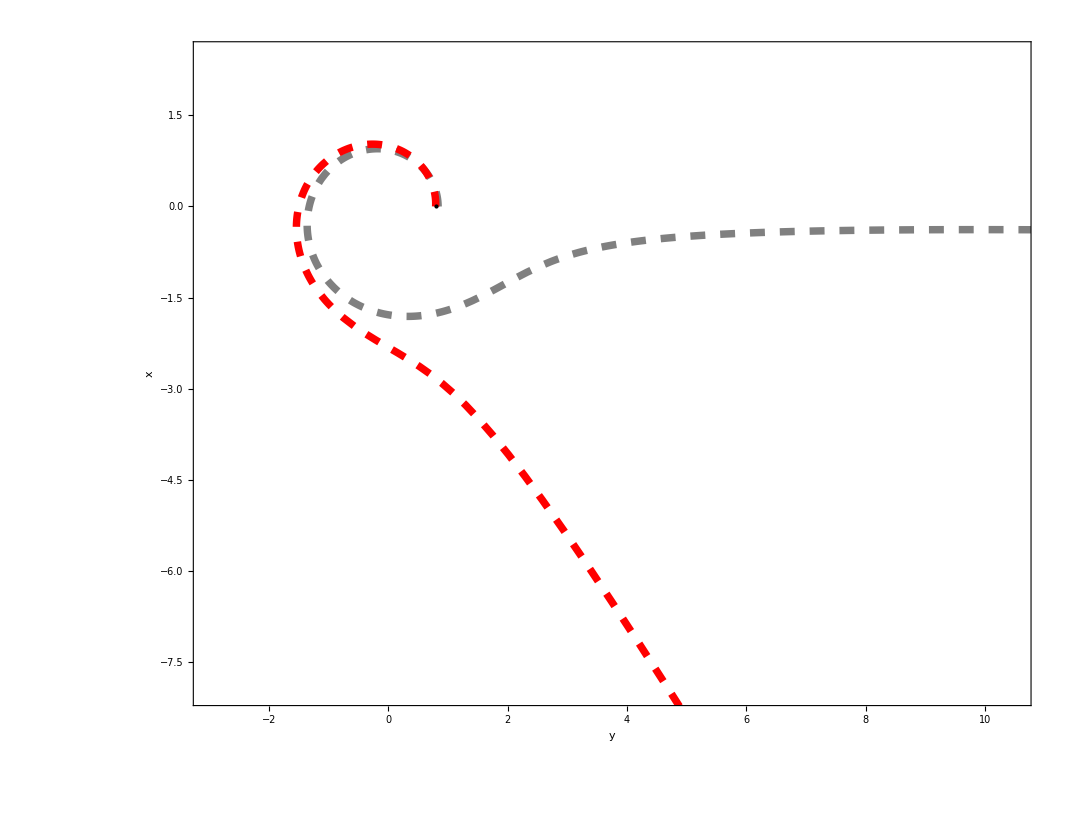

```mathematica
Plot01=Show[{Plot1,Plot2,Graphics[{Black,PointSize[Large],Point[{solri1[ts] Cos[solthi1[ts]],solri1[ts] Sin[solthi1[ts]]}]}]},PlotRange->{{-3,10.5},{-8,2.5}}]
```

General::munfl: Exp[-60926.6] is too small to represent as a normalized machine number; precision may be lost.

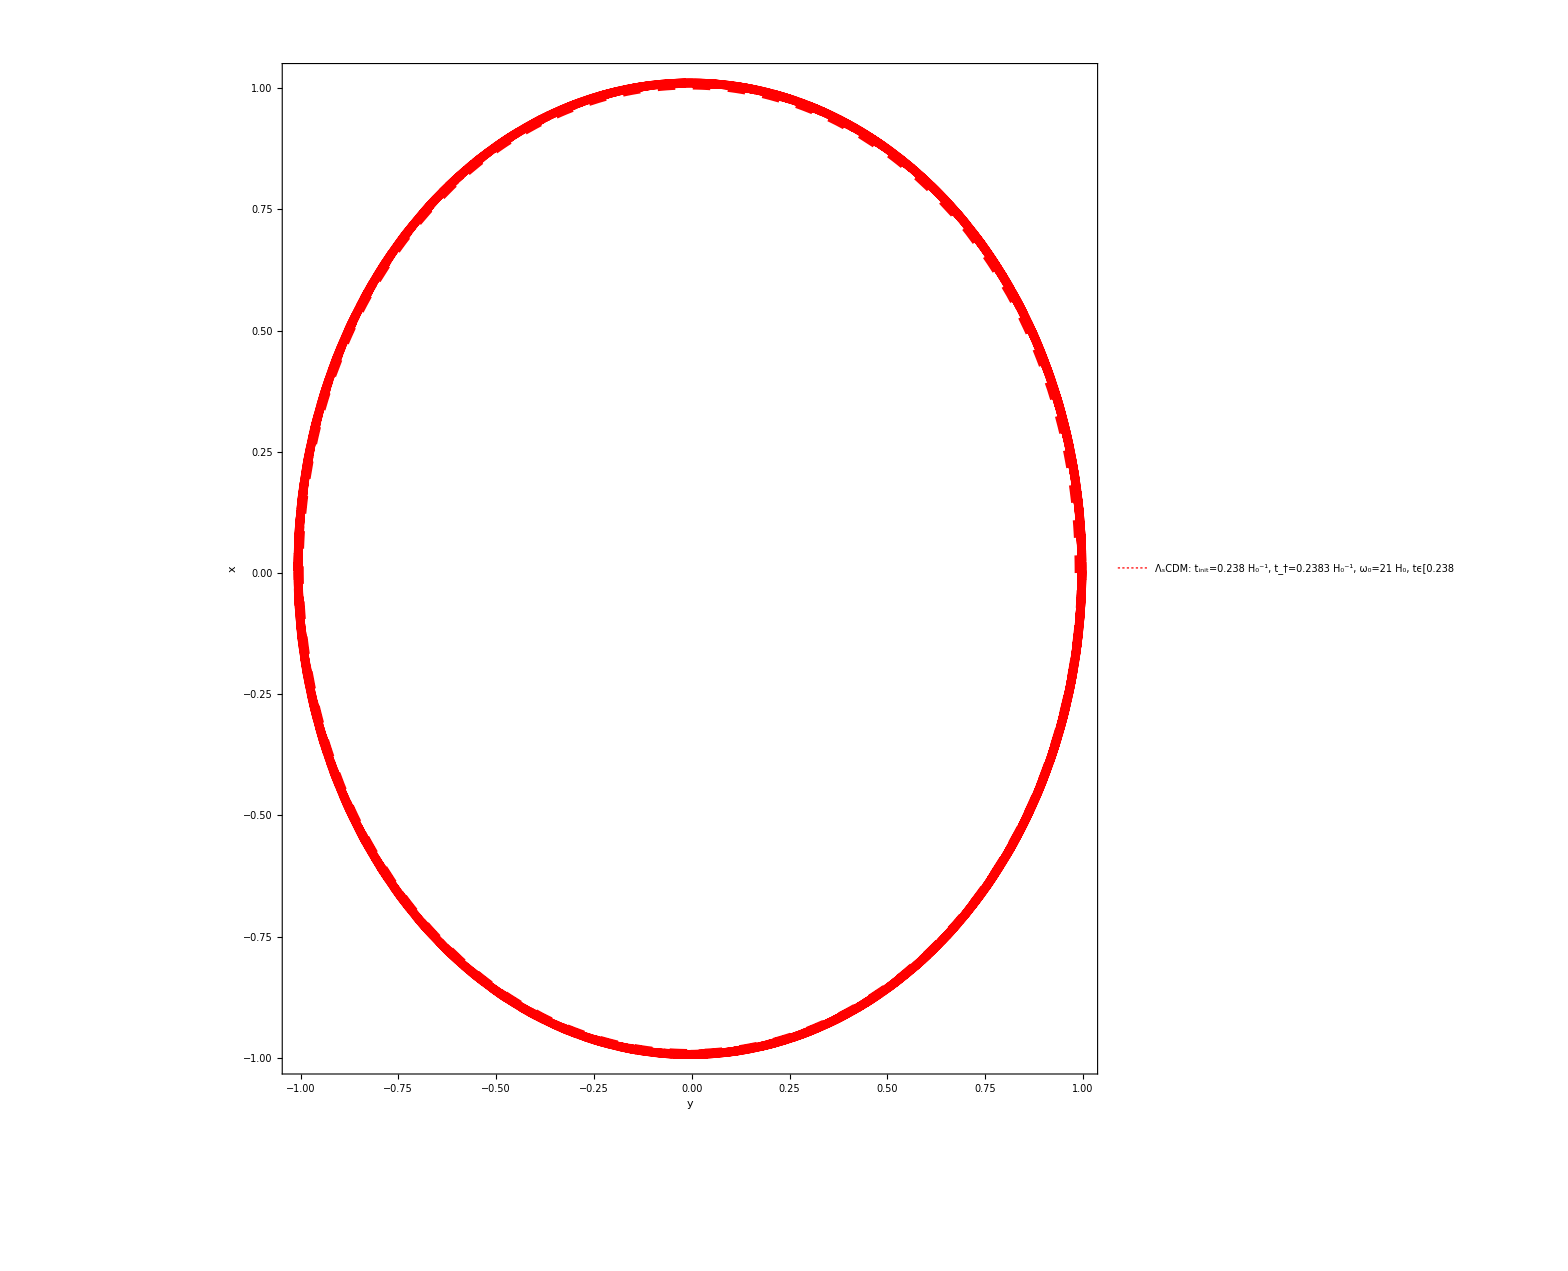

```mathematica
Off[NIntegrate::nlim,FunctionInterpolation::ncvb,NIntegrate::slwcon,NIntegrate::ncvb];
Clear[H0tinit,omegam,om];
H0tinit=0.238;  omegam=0.29;  om=5;



tend=10; ti=1;  (* time limits *)
ts=0.2383/0.238;
a=Piecewise[{{(omegam/(1-omegam))^(1/3)Sin[3/2 H0tinit √(1-omegam)t]^(2/3),t<=ts},{(omegam/(1-omegam))^(1/3)Sinh[3/2 H0tinit √(1-omegam)(t-ts)+ArcSinh[Sin[3/2 H0tinit √(1-omegam)ts]]]^(2/3),t>=ts}}];  

ff=1/2 (H0tinit)^2 omegam a (-3/a^4+(2 (1-omegam) 1/(10^-5 √Pi)Exp[-((1/((omegam/(1-omegam))^(1/3)Sin[3/2 H0tinit √(1-omegam)ts]^(2/3))-1/a)/10^-5)^2])/(omegam a^2))+(H0tinit)^2 (-(1-omegam)+omegam/a^3+2 (1-omegam) (1/2+1/2 Tanh[1/10^-5 (1/((omegam/(1-omegam))^(1/3)Sin[3/2 H0tinit √(1-omegam)ts]^(2/3))-1/a)]));
par=om^2 rr - om^2 -ff  rr^4 /. t->ti; (* factor proportional to the effective force in the geodesic equation *)
ss=Part[Solve[par==0,rr] //N,2,1,2];  (* find initial equilibrium point to use in the initial conditions to avoid oscillations in the solution *)
solution1=NDSolve[{r''[t]+(om^2/r[t]^2)(1-1/r[t])-ff r[t]==0,r[ti]==ss,r'[ti]==0},r,{t,ti,tend},MaxSteps->300000]; (* find radial geodesic *)

solr1[t1_]:=Part[Evaluate[r[t]/.solution1] /. t->t1,1];
solth1[t1_]:=NIntegrate[om/solr1[t]^2,{t,ti,t1}];
solri1=FunctionInterpolation[solr1[t],{t,ti,tend}];
solthi1=FunctionInterpolation[solth1[tt],{tt,ti,tend}];

t1=1;t2=10;
plor1=ParametricPlot[{solri1[t] Cos[solthi1[t]],solri1[t] Sin[solthi1[t]]},{t,t1,t2},AspectRatio->Automatic,PlotRange->All,Frame->True,FrameLabel->{"x/r_0","y/r_0"},PlotStyle -> {RGBColor[1,0,0],Dashing[0.01],Thickness[0.005]},PlotLegends->Placed[LineLegend[{Style["Λ_sCDM: \!\(\*SubscriptBox[\(t\), \(init\)]\)=0.238 \!\(\*SuperscriptBox[SubscriptBox[\(H\), \(0\)],\(-1\)]\), t_†=0.2383 H_0^-1, \!\(\*SubscriptBox[\(ω\), \(0\)]\)=21 H_0, tϵ[0.238\!\(\*SuperscriptBox[SubscriptBox[\(H\), \(0\)], \(-1\)]\),2.38 \!\(\*SuperscriptBox[SubscriptBox[\(H\), \(0\)], \(-1\)]\)]",FontSize->25]},LabelStyle->{FontSize->25}],{Left,Top}]];


Plot3=Show[plor1,PlotRange->All,Frame->True,FrameLabel->{"y","x"},BaseStyle->{Large,FontFamily->"Times",Italic},LabelStyle->Directive[Black,Large]]
```

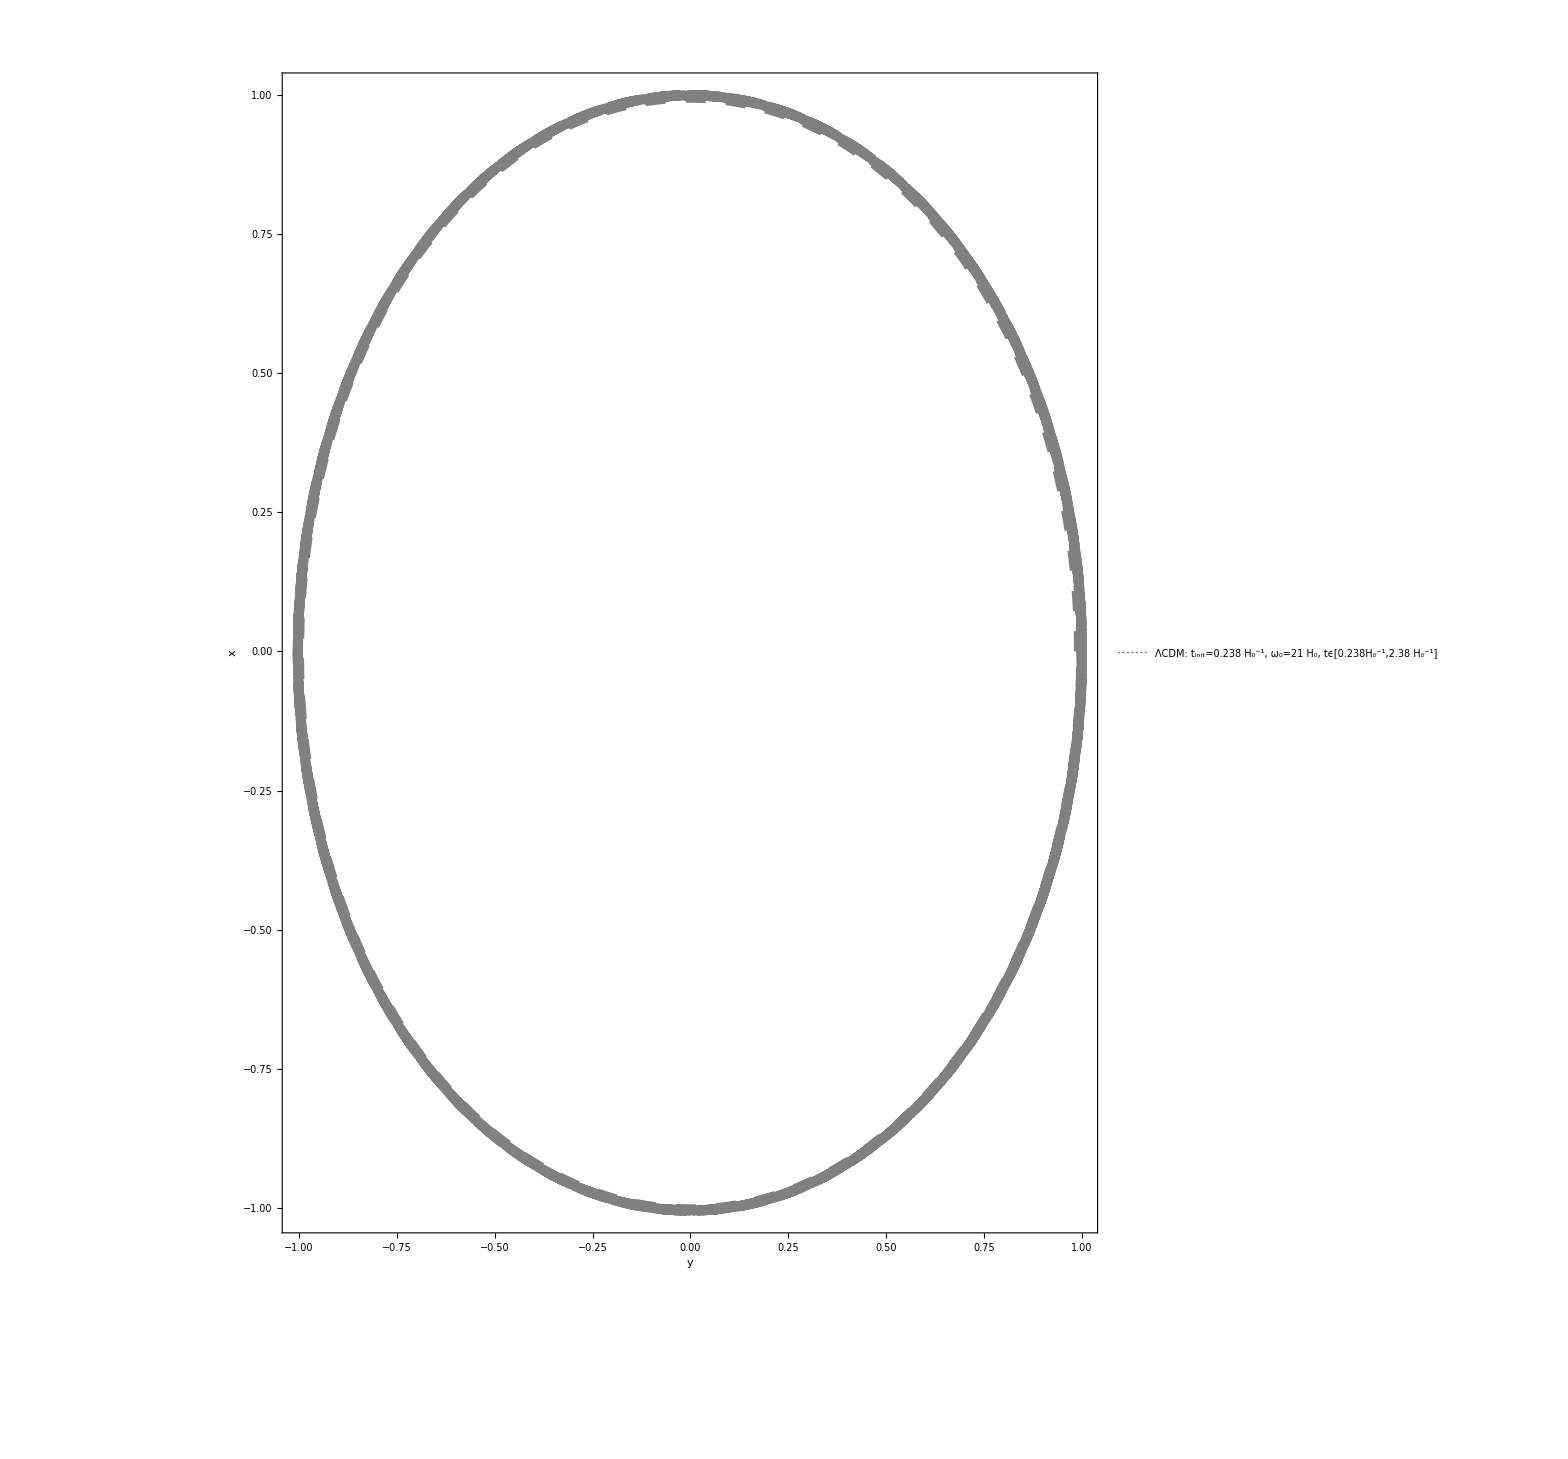

```mathematica
Off[NIntegrate::nlim,FunctionInterpolation::ncvb,NIntegrate::slwcon,NIntegrate::ncvb];
Clear[H0tinit,omegam,om];
H0tinit=0.238;  omegam=0.29;  om=5;


tend=10; ti=1;  (* time limits *)

a=(omegam/(1-omegam))^(1/3)Sinh[3/2 H0tinit √(1-omegam)t]^(2/3);  

ff=H0tinit^2(1+(-1-1/(2 a^3)) omegam);
par=om^2 rr - om^2 -ff  rr^4 /. t->ti; (* factor proportional to the effective force in the geodesic equation *)
ss=Part[Solve[par==0,rr] //N,2,1,2];  (* find initial equilibrium point to use in the initial conditions to avoid oscillations in the solution *)
solution1=NDSolve[{r''[t]+(om^2/r[t]^2)(1-1/r[t])-ff r[t]==0,r[ti]==ss,r'[ti]==0},r,{t,ti,tend},MaxSteps->300000]; (* find radial geodesic *)

solr1[t1_]:=Part[Evaluate[r[t]/.solution1] /. t->t1,1];
solth1[t1_]:=NIntegrate[om/solr1[t]^2,{t,ti,t1}];
solri1=FunctionInterpolation[solr1[t],{t,ti,tend}];
solthi1=FunctionInterpolation[solth1[tt],{tt,ti,tend}];

t1=1;t2=10;
plor1=ParametricPlot[{solri1[t] Cos[solthi1[t]],solri1[t] Sin[solthi1[t]]},{t,t1,t2},AspectRatio->Automatic,PlotRange->All,Frame->True,FrameLabel->{"x/\!\(\*SubscriptBox[\(r\), \(0\)]\)","y/\!\(\*SubscriptBox[\(r\), \(0\)]\)"},PlotStyle->{Gray,Dashing[0.01],Thickness[0.005]},PlotLegends->Placed[LineLegend[{Style["ΛCDM: \!\(\*SubscriptBox[\(t\), \(init\)]\)=0.238 \!\(\*SuperscriptBox[SubscriptBox[\(H\), \(0\)], \(-1\)]\), \!\(\*SubscriptBox[\(ω\), \(0\)]\)=21 H_0, tϵ[0.238\!\(\*SuperscriptBox[SubscriptBox[\(H\), \(0\)], \(-1\)]\),2.38 \!\(\*SuperscriptBox[SubscriptBox[\(H\), \(0\)], \(-1\)]\)]",FontSize->25]},LabelStyle->{FontSize->25}],{Left,Top}]];



Plot4=Show[plor1,PlotRange->All,Frame->True,FrameLabel->{"y","x"},BaseStyle->{Large,FontFamily->"Times",Italic},LabelStyle->Directive[Black,Large]]
```

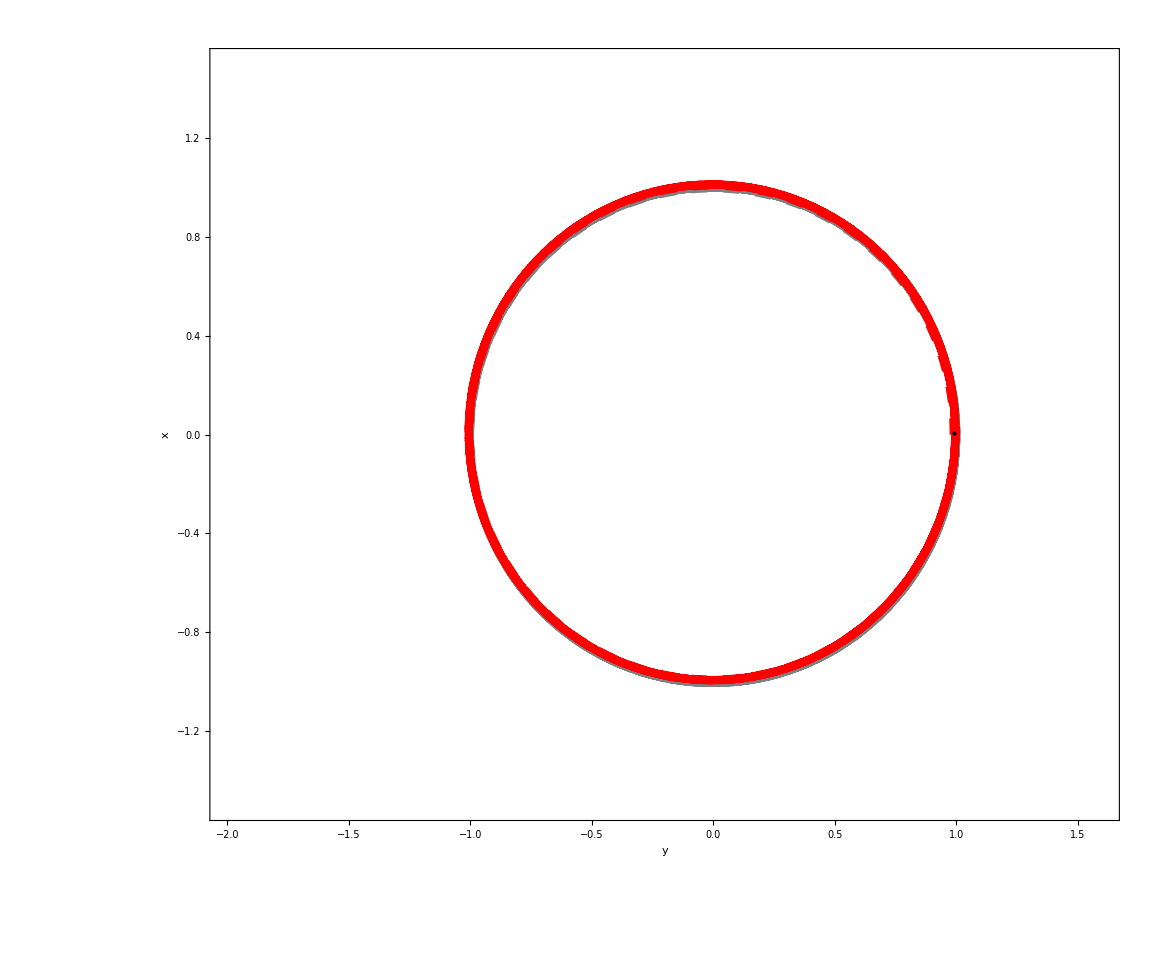

```mathematica
Plot02=Show[{Plot4,Plot3,Graphics[{Black,PointSize[Large],Point[{solri1[ts] Cos[solthi1[ts]],solri1[ts] Sin[solthi1[ts]]}]}]},PlotRange->{{-2,1.6},{-1.5,1.5}}]
```

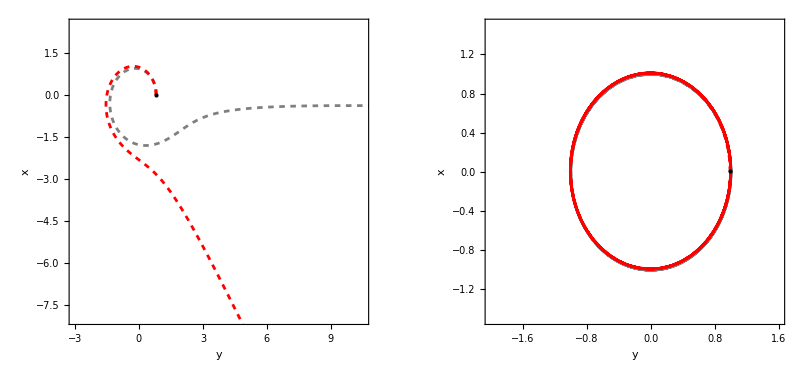

```mathematica
GraphicsRow[{Plot01,Plot02},ImageSize->600,Spacings->30]
```